## 1 D

```mathematica
p1DA[x_]:=x;
p1DB[x_]:=-x;
p1DC[x_]:=1.5x;
p1DD[x_]:=1.5x+2.3;
p1DE[x_]:=1.5 x^2+2.3x-1.1;
p1DF[x_]:=1.5 x^3+2.3 x^2-1.1x+3.7;
p1DG[x_]:=1.5 x^4+2.3 x^3-1.1 x^2+3.7x-4.5;
```

```mathematica
polynomials1D={p1DA,p1DB,p1DC,p1DD,p1DE,p1DF,p1DG};
```

```mathematica
print1D[p_]:=
Grid[{
{Style[StringReplace[ToString[p],"p1D"->""],Bold,20]},
{{Min[#],Max[#]}&[Table[p[x],{x,-10,10,20/19}]]},
{Style[p[x]//TraditionalForm,8]},
{Plot[p[x],{x,-10,10},PlotStyle->Thick]}
}]
```

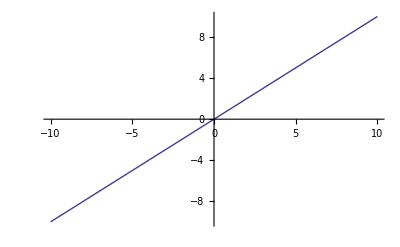
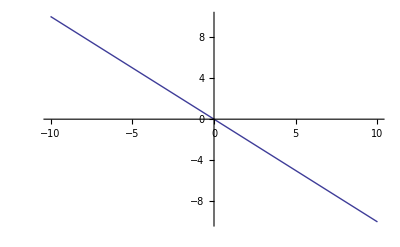
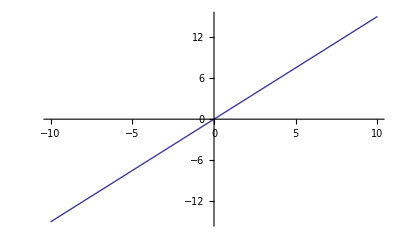
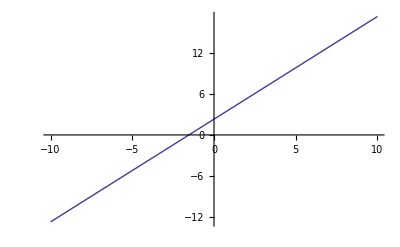
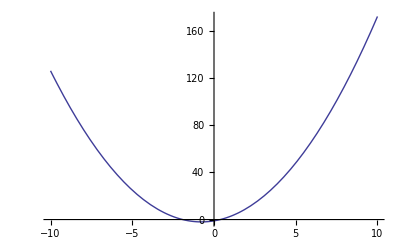
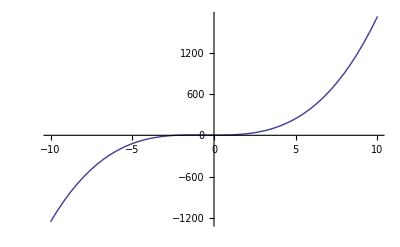
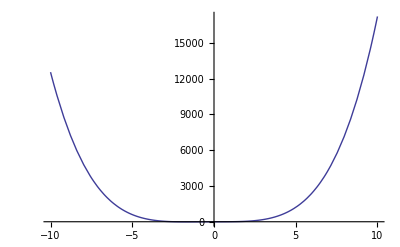
A
{-10,10}
x
-Graphics- | B
{-10,10}
-x
-Graphics- | C
{-15.,15.}
1.5 x
-Graphics- | D
{-12.7,17.3}
1.5 x+2.3
-Graphics-
E
{-1.89501,171.9}
1.5 x^2+2.3 x-1.1
-Graphics- | F
{-1255.3,1722.7}
1.5 x^3+2.3 x^2-1.1 x+3.7
-Graphics- | G
{-12.8152,17222.5}
1.5 x^4+2.3 x^3-1.1 x^2+3.7 x-4.5
-Graphics- |

```mathematica
Grid[Partition[(print1D[#]&/@polynomials1D)~Join~{" "},4]]
```

```mathematica
Export["pokus.pdf",%]
```

pokus.pdf

## 2 D

```mathematica
p2DA[x_,y_]:=x y
p2DB[x_,y_]:=-x y
p2DC[x_,y_]:=1.5x y
p2DD[x_,y_]:=1.5x y+2.3x
p2DE[x_,y_]:=1.5x y+2.3x+y
p2DF[x_,y_]:=1.5x y+2.3x-1.1y
p2DG[x_,y_]:=1.5x y^2+2.3x-1.1y
p2DH[x_,y_]:=1.5x y^2+2.3x y-1.1y
p2DI[x_,y_]:=1.5x y^2+2.3x y-1.1 y^2
p2DJ[x_,y_]:=x y^2+x y-y
p2DK[x_,y_]:=x y^2+x y-y^2
```

```mathematica
polynomials2D={p2DA,p2DB,p2DC,p2DD,p2DE,p2DF,p2DG,p2DH,p2DI,p2DJ,p2DK};
```

```mathematica
print2D[p_]:=
Grid[{
{Style[StringReplace[ToString[p],"p2D"->""],Bold,20]},
{N[{Min[#],Max[#]}]&[Table[p[x,y],{x,-10,10,20/6},{y,-10,10,20/6}]]},
{Style[p[x,y]//TraditionalForm,12]},
{ContourPlot[p[x,y],{x,-10,10},{y,-10,10},ContourLabels->True,ColorFunction->"Rainbow",ImageSize->250]}
}]
```

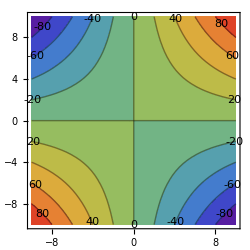
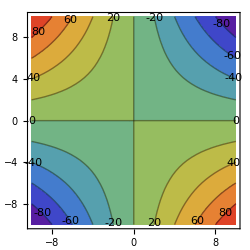
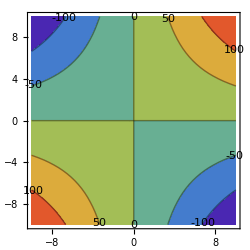
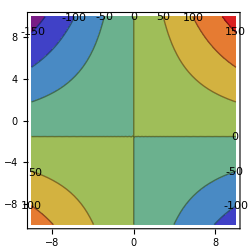
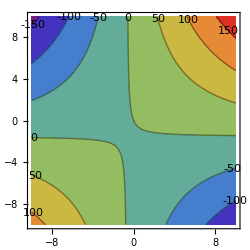
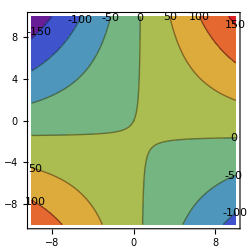
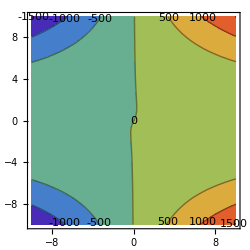
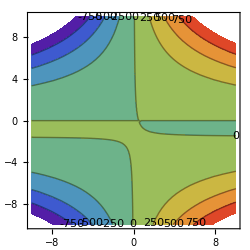
A
{-100.,100.}
x y
-Graphics- | B
{-100.,100.}
-x y
-Graphics- | C
{-150.,150.}
1.5 x y
-Graphics- | D
{-173.,173.}
1.5 x y+2.3 x
-Graphics-
E
{-163.,183.}
1.5 x y+2.3 x+y
-Graphics- | F
{-184.,162.}
1.5 x y+2.3 x-1.1 y
-Graphics- | G
{-1534.,1534.}
1.5 x y^2+2.3 x-1.1 y
-Graphics- | H
{-1741.,1719.}
1.5 x y^2+2.3 x y-1.1 y
-Graphics-
I
{-1840.,1620.}
1.5 x y^2+2.3 x y-1.1 y^2
-Graphics- | J
{-1110.,1090.}
x y^2+x y-y
-Graphics- | K
{-1200.,1000.}
x y^2+x y-y^2
-Graphics- |

```mathematica
Grid[Partition[(print2D[#]&/@polynomials2D)~Join~{" "},4]]
```

```mathematica
Export["2D.pdf",%]
```

2D.pdf

## 3 D

```mathematica
p3DA[x_,y_,z_]:=x y z
p3DB[x_,y_,z_]:=-x y z
p3DC[x_,y_,z_]:=1.5x y z
p3DD[x_,y_,z_]:=1.5x y+2.3x - 1.1z
p3DE[x_,y_,z_]:=1.5x y+2.3x+y z-1.1z
p3DF[x_,y_,z_]:=1.5 x y z+2.3x-1.1y-1.1z
p3DG[x_,y_,z_]:=1.5 x y^2 z+2.3x-1.1y
p3DH[x_,y_,z_]:=1.5 x y^2 z+2.3 x y z-1.1y+5.3
p3DI[x_,y_,z_]:=1.5 x y^2+2.3 x y z-1.1 y^2
p3DJ[x_,y_,z_]:=x y^2+x z-y z
p3DK[x_,y_,z_]:=x y^2 z+z y-x y
```

```mathematica
polynomials3D={p3DA,p3DB,p3DC,p3DD,p3DE,p3DF,p3DG,p3DH,p3DI,p3DJ,p3DK};
```

```mathematica
Grid[Transpose@{
Style[StringReplace[ToString[#],"p3D"->""],Bold]&/@polynomials3D,
(#[x,y,z]//TraditionalForm)&/@polynomials3D,
N[Min[#]]&[Table[#[x,y,z],{x,-10,10,20/6},{y,-10,10,20/6},{z,-10,10,20/6}]]&/@polynomials3D,
N[Max[#]]&[Table[#[x,y,z],{x,-10,10,20/6},{y,-10,10,20/6},{z,-10,10,20/6}]]&/@polynomials3D
},Frame->All]
```

A | x y z | -1000. | 1000.
B | -x y z | -1000. | 1000.
C | 1.5 x y z | -1500. | 1500.
D | 1.5 x y+2.3 x-1.1 z | -184. | 184.
E | 1.5 x y+2.3 x+y z-1.1 z | -262. | 262.
F | 1.5 x y z+2.3 x-1.1 y-1.1 z | -1545. | 1545.
G | 1.5 x y^2 z+2.3 x-1.1 y | -15034. | 15034.
H | 1.5 x y^2 z+2.3 x y z-1.1 y+5.3 | -17305.7 | 17294.3
I | 1.5 x y^2+2.3 x y z-1.1 y^2 | -3910. | 3690.
J | x y^2+x z-y z | -1200. | 1200.
K | x y^2 z-x y+y z | -10200. | 10000.

```mathematica
TeXForm[%]
```

\begin{array}{cccc}
 \text{A} & x y z & -1000. & 1000. \\
 \text{B} & -x y z & -1000. & 1000. \\
 \text{C} & 1.5 x y z & -1500. & 1500. \\
 \text{D} & 1.5 x y+2.3 x-1.1 z & -184. & 184. \\
 \text{E} & 1.5 x y+2.3 x+y z-1.1 z & -262. & 262. \\
 \text{F} & 1.5 x y z+2.3 x-1.1 y-1.1 z & -1545. & 1545. \\
 \text{G} & 1.5 x y^2 z+2.3 x-1.1 y & -15034. & 15034. \\
 \text{H} & 1.5 x y^2 z+2.3 x y z-1.1 y+5.3 & -17305.7 & 17294.3 \\
 \text{I} & 1.5 x y^2+2.3 x y z-1.1 y^2 & -3910. & 3690. \\
 \text{J} & x y^2+x z-y z & -1200. & 1200. \\
 \text{K} & x y^2 z-x y+y z & -10200. & 10000.
\end{array}

```mathematica
plots=Table[{z,Plot3D[p3DH[x,y,z],{x,-10,10},{y,-10,10},ColorFunction->"Rainbow",PlotRange->{-17300,17300},ImageSize->400]},{z,-10,10,0.1}];
```

```mathematica
Animate[plots[[i]],{i,Range[Length[plots]]}]
```

```mathematica
p3DH[10,10,9.1]
```

15737.3

## 4 D

```mathematica
p4DA[x_,y_,z_,w_]:=x y z w
p4DB[x_,y_,z_,w_]:=-x y z w
p4DC[x_,y_,z_,w_]:=1.5x y z w
p4DD[x_,y_,z_,w_]:=1.5x y+2.3x - 1.1z w
p4DE[x_,y_,z_,w_]:=1.5x y+2.3x y z w-1.1z
p4DF[x_,y_,z_,w_]:=1.5 x y z+2.3x-1.1y-1.1w
p4DG[x_,y_,z_,w_]:=1.5 x y^2 z w+2.3x-1.1y
p4DH[x_,y_,z_,w_]:=x y z+x- y-w
p4DI[x_,y_,z_,w_]:=x y^2 z w+x-y w
p4DFC55[x_,y_,z_,w_]:= Exp[-1.3670864746106228*y^2]*x*(2.434541692158718*Exp[-z^2]-0.3937877771163354*Sin[1-x])
```

```mathematica
polynomials4D={p4DA,p4DB,p4DC,p4DD,p4DE,p4DF,p4DG,p4DH,p4DI,p4DFC55};
```

```mathematica
Grid[Transpose@{
Style[StringReplace[ToString[#],"p4D"->""],Bold]&/@polynomials4D,
(#[Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]]//TraditionalForm)&/@polynomials4D,
N[Min[#]]&[Table[#[x,y,z,w],{x,-1,1,2/4},{y,-1,1,2/4},{z,-1,1,2/4},{w,-1,1,2/4}]]&/@polynomials4D,
N[Max[#]]&[Table[#[x,y,z,w],{x,-1,1,2/4},{y,-1,1,2/4},{z,-1,1,2/4},{w,-1,1,2/4}]]&/@polynomials4D
},Frame->All]
```

A | x_1 x_2 x_3 x_4 | -1. | 1.
B | -x_1 x_2 x_3 x_4 | -1. | 1.
C | 1.5 x_1 x_2 x_3 x_4 | -1.5 | 1.5
D | 1.5 x_2 x_1+2.3 x_1-1.1 x_3 x_4 | -4.9 | 4.9
E | 1.5 x_1 x_2+2.3 x_1 x_3 x_4 x_2-1.1 x_3 | -4.9 | 4.9
F | 1.5 x_2 x_3 x_1+2.3 x_1-1.1 x_2-1.1 x_4 | -6. | 6.
G | 1.5 x_1 x_3 x_4 x_2^2-1.1 x_2+2.3 x_1 | -4.9 | 4.9
H | x_2 x_3 x_1+x_1-x_2-x_4 | -4. | 4.
I | x_1 x_3 x_4 x_2^2-x_4 x_2+x_1 | -3. | 3.
FC55 | ⅇ^(-1.36709 x_2^2) x_1 (2.43454 ⅇ^(-x_3^2)-0.393788 sin(1-x_1)) | -2.07647 | 2.43454

```mathematica
TeXForm[%]
```

\begin{array}{cccc}
 \text{A} & x_1 x_2 x_3 x_4 & -1. & 1. \\
 \text{B} & -x_1 x_2 x_3 x_4 & -1. & 1. \\
 \text{C} & 1.5 x_1 x_2 x_3 x_4 & -1.5 & 1.5 \\
 \text{D} & 1.5 x_2 x_1+2.3 x_1-1.1 x_3 x_4 & -4.9 & 4.9 \\
 \text{E} & 1.5 x_1 x_2+2.3 x_1 x_3 x_4 x_2-1.1 x_3 & -4.9 & 4.9 \\
 \text{F} & 1.5 x_2 x_3 x_1+2.3 x_1-1.1 x_2-1.1 x_4 & -6. & 6. \\
 \text{G} & 1.5 x_1 x_3 x_4 x_2^2-1.1 x_2+2.3 x_1 & -4.9 & 4.9 \\
 \text{H} & x_2 x_3 x_1+x_1-x_2-x_4 & -4. & 4. \\
 \text{I} & x_1 x_3 x_4 x_2^2-x_4 x_2+x_1 & -3. & 3. \\
 \text{FC55} & e^{-1.36709 x_2^2} x_1 \left(2.43454 e^{-x_3^2}-0.393788 \sin \left(1-x_1\right)\right) & -2.07647 & 2.43454
\end{array}

```mathematica
plots=Table[{z,Plot3D[p4DFC55[x,y,z,0],{x,-1,1},{y,-1,1},ColorFunction->"Rainbow",PlotRange->{-2.1,2.5},ImageSize->300]},{z,-1,1,0.01}];
```

```mathematica
Animate[plots[[i]],{i,Range[Length[plots]]}]
```

```mathematica
Manipulate[Plot[p4DFC55[x,y,z,0],{z,-10,10},PlotRange->{-3,3}],{x,-1,1},{y,-1,1}]
```

```mathematica
p4DFC55[0,0,0,0]
```

0.